```mathematica
xd[u_,v_] := 4+(3+Cos[v])Sin[u]
yd[u_,v_]:= 4+(3+Cos[v])Cos[u]
zd[u_,v_] := 4+ Sin[v]
f1[x_,y_] := 5*Sin[(x^2 - y^2)/10]
P11 = Plot3D[f1[x,y],{x,0,8},{y,0,8},PlotPoints->{40,50},PlotStyle->Blue]
```

-Graphics3D-

```mathematica
xd1[u_,v_] := 4+(3+Cos[v])Sin[u]
yd1[u_,v_] := 4+(3+Cos[v])Cos[u]
zd1[u_,v_] := 4+ Sin[v]
pd1[u_,v_] := {xd1[u,v],yd1[u,v],zd1[u,v]}
P12 = ParametricPlot3D[pd1[u,v],{u,0,2Pi},{v,0,2Pi},PlotStyle->Green]
```

-Graphics3D-

```mathematica
Show[{P12,P11},PlotRange ->{{0,8},{0,8},{-5,8}},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
xp2[t_] := 3*Cos[t]+4
yp2[t_] := 4*Cos[t]+3*Sin[t]+3
zp2[t_] := 4*Sin[t]
P2[t_] := {xp2[t],yp2[t],zp2[t]}
P2x = ParametricPlot3D[P2[t],{t,0,8},PlotStyle->{Orange,Thickness->0.05}]
```

-Graphics3D-

```mathematica
Show[{P12,P11,P2x},PlotRange ->{{-2,10},{-2,10},{-8,8}},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
f3[x_,y_,a_] := Sin[a*x*y*2]*Exp[-x^2-y^2]
plot3[a_] := Plot3D[f3[x,y,a],{x,-1,1},{y,-1,1},PlotPoints->30]
Manipulate[plot3[a],{a,1,5,o.25}]
```

```mathematica
Table4 := Table[plot3[a4],{a4,1,5,0.25}]
ListAnimate[Table4,AnimationRunning->False]
```

```mathematica
{Slider[Dynamic[a5],{1,5,0.1}],Dynamic[a5]}
```

{,}

```mathematica
Dynamic[plot3[a5]]
```

```mathematica
Toggler[Dynamic[a6],{1,5,4,3,2,-1}]
```

```mathematica
Dynamic[plot3[a6]]
```

```mathematica
xp6[u_,v_,a_] := 4+(3+Cos[a*v])Sin[u]
yp6[u_,v_] :=4+(3+Cos[v])Cos[u]
zp6[u_,v_] := 4+Sin[v]
x6[u_,v_,a_] := {xp6[u,v,a],yp6[u,v],zp6[u,v]}
P6 = Animate[ParametricPlot3D[x6[u,v,a],{u,0,2Pi},{v,0,2Pi}],{a,1,4,0.25},AnimationRunning->False]
```

```mathematica
Table8:= Table[P6[a8],{a8,1,4,0.25}]
ListAnimate[Table8,AnimationRunning->False]
```

```mathematica
{Slider[Dynamic[a9],{1,4,0.25}],Dynamic[a9]}
Dynamic[P6[a9]]
```

{,}

```mathematica
Toggler[Dynamic[a10],{1,0,-1,2,3,4,0}]
Dynamic[P6[a10]]
```

```mathematica
su1[x_,y_,s_] := s*(x^2 - y^2)/10
x11[u_,v_,s_] := Cos[v] Sin[u]*s
y11[u_,v_,s_] := s/3* Cos[v] Cos[u]
z11[v_] := 6*Sin[v]
p11[u_,v_,s_] := {x11[u,v,s],y11[u,v,s],z11[v]}
plot11x[s_] := Plot3D[su1[x,y,s],{x,-4,4},{y,-4,4},PlotPoints->100]

plot11y[s_] := ParametricPlot3D[p11[u,v,s],{u,-4,4},{v,-4,4},PlotStyle ->LightRed,PlotPoints->100]
plot11[s_] := Show[{plot11x[s],plot11y[s]},PlotRange->{{-5,5},{-5,5},{-10,10}}]
Manipulate[plot11[s],{s,1,5,0.25}]
```

```mathematica
x12[u_,v_] := Cos[v]Sin[u]
y12[u_,v_] := 1/2*Cos[v]Cos[u/2]
z12[v_] := 6*Sin[v]
su12[u_,v_] := {x12[u,v],y12[u,v],z12[v]}
plotsu12p[o_] := ParametricPlot3D[su12[u,v],{u,-4,4},{v,-4,4},PlotStyle->{Red,Opacity[o]},BoxRatios->{1,1,1},Mesh->False]
Toggler[Dynamic[o],{0.1,0.2,0.3,0.5,0.7,0.95}]
```

```mathematica
Dynamic[plotsu12p[o]]
```

```mathematica
plotsu13p[c_] := ParametricPlot3D[su12[u,v],{u,-4,4},{v,-4,4},PlotStyle->{c,Opacity[0.8]},BoxRatios->{1,1,1},Mesh->False]
Toggler[Dynamic[c],{Yellow,Green,Blue,Brown,Pink,Purple}]
Dynamic[plotsu13p[c]]
```

```mathematica
data14 = {{1,1},{-2,3},{-1,-3},{7,0},{3,1},{2,2}}
f14 := Interpolation[data14,Method->"Spline"]
minx = Min[Transpose[data14][[1]]]
```

{{1,1},{-2,3},{-1,-3},{7,0},{3,1},{2,2}}

-2

```mathematica
maxx = Max[Transpose[data14][[1]]]
```

7

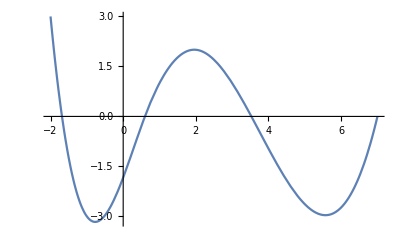

```mathematica
plot141 = Plot[f14[x],{x,minx,maxx}]
```

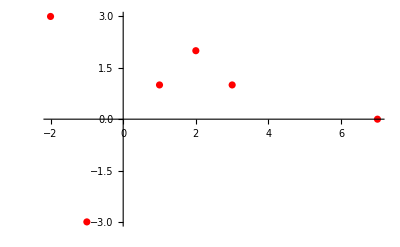

```mathematica
plot142 = ListPlot[data14,PlotStyle->{0.03,Red}]
```

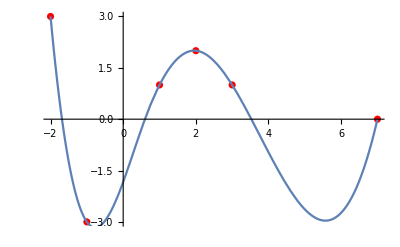

```mathematica
Show[plot142,plot141]
```

```mathematica
x15=Transpose[data14][[1]]
```

{1,-2,-1,7,3,2}

```mathematica
y15=Transpose[data14][[2]]
```

{1,3,-3,0,1,2}

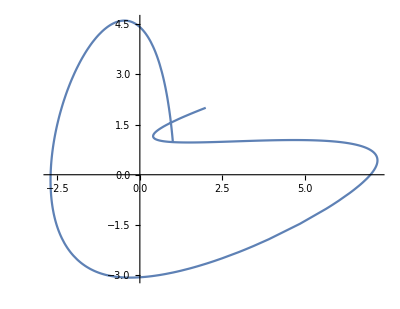

```mathematica
sx15 := Interpolation[x15,Method->"Spline"]
sy15 := Interpolation[y15,Method->"Spline"]
spline15[t_] := {sx15[t],sy15[t]}
plot15 = ParametricPlot[spline15[t],{t,1,Length[x15]}]
```

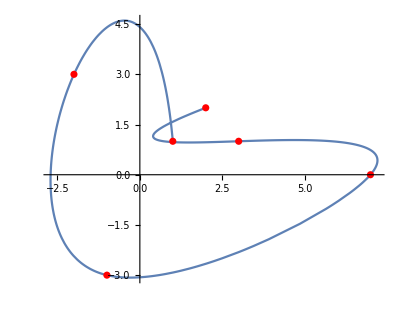

```mathematica
Show[plot15,plot142]
```

```mathematica
data16 = Table[{1.0*Sin[i],Cos[i*0.9]},{i,8}]
```

{{0.841471,0.62161},{0.909297,-0.227202},{0.14112,-0.904072},{-0.756802,-0.896758},{-0.958924,-0.210796},{-0.279415,0.634693},{0.656987,0.999859},{0.989358,0.608351}}

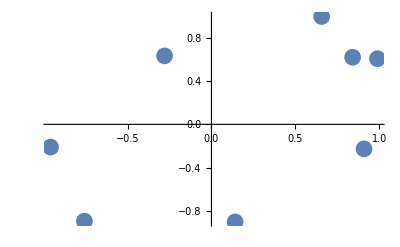

```mathematica
plot161 = ListPlot[data16, PlotStyle->PointSize[0.03]]
f16 := Interpolation[data16,Method->"Spline"]
```

```mathematica
min16 = Min[Transpose[data16][[1]]]
max16 = Max[Transpose[data16][[1]]]
```

-0.958924

0.989358

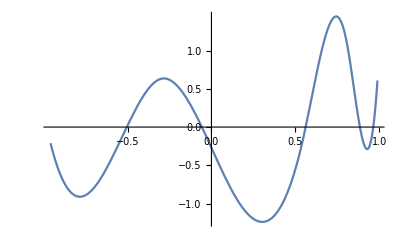

```mathematica
plot162 = Plot[f16[x2],{x2,min16,max16}]
```

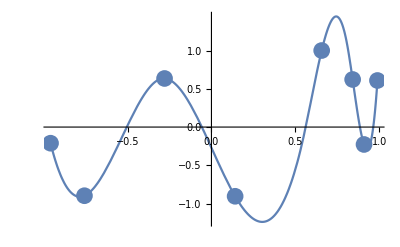

```mathematica
Show[plot161,plot162,PlotRange->{{2,-2},{2,-2}}]
```

{0.841471,0.909297,0.14112,-0.756802,-0.958924,-0.279415,0.656987,0.989358}

{0.62161,-0.227202,-0.904072,-0.896758,-0.210796,0.634693,0.999859,0.608351}

InterpolatingFunction[…]

InterpolatingFunction[…]

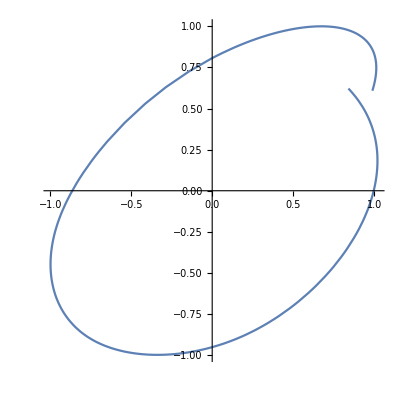

```mathematica
x16 = Transpose[data16][[1]]
y16 = Transpose[data16][[2]]
sx16 = Interpolation[x16,Method->"Spline"]
sy16 = Interpolation[y16, Method->"Spline"]
spline16[t_] := {sx16[t],sy16[t]}
plot163 = ParametricPlot[spline16[t],{t,1,Length[x16]}]
```

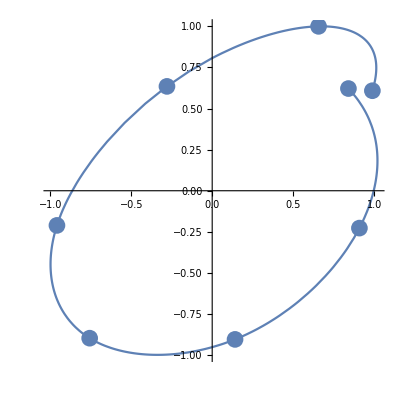

```mathematica
Show[plot163,plot161]
```

```mathematica
data18 = {{1,1,1},{2,3,1},{1,3,2},{4,3,3},{4,4,4},{5,3,2},{7,5,6},{5,5,5}}
x18 = Transpose[data18][[1]]
y18 = Transpose[data18][[2]]
z18 = Transpose[data18][[3]]
sx18 =Interpolation[x18,Method->"Spline"]
sy18 = Interpolation[y18,Method->"Spline"]
sz18 = Interpolation[z18,Method->"Spline"]
spline18[t_] := {sx18[t],sy18[t],sz18[t]}
```

{{1,1,1},{2,3,1},{1,3,2},{4,3,3},{4,4,4},{5,3,2},{7,5,6},{5,5,5}}

{1,2,1,4,4,5,7,5}

{1,3,3,3,4,3,5,5}

{1,1,2,3,4,2,6,5}

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
plot181 = ListPointPlot3D[data18,PlotStyle->{PointSize[0.03],Red}]
```

-Graphics3D-

```mathematica
plot182 = ParametricPlot3D[spline18[t],{t,1,Length[x18]}]
```

-Graphics3D-

```mathematica
Show[plot181,plot182]
```

-Graphics3D-